```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

```mathematica
binent[x_]:=-x Log[x] - (1-x)Log[1-x]
```

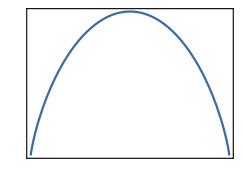

```mathematica
fs1 = 15;
fs2 = 10;
fig = Plot[binent[x], {x, 0, 1},

PlotStyle->col1,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,

FrameLabel->{MaTeX["x", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{h}\\left(x\\right)", ContentPadding->False, FontSize->fs1]},


FrameTicks->{{{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{Log[2], MaTeX["\\log 2" , ContentPadding->False, FontSize->fs2]},
{Log[2]/2, MaTeX["\\frac{\\log 2}{2} " , ContentPadding->False, FontSize->fs2]}
(*{0.2, MaTeX["0.2" , ContentPadding->False, FontSize->fs2]},
{0.4, MaTeX["0.4" , ContentPadding->False, FontSize->fs2]},
{0.6, MaTeX["0.6" , ContentPadding->False, FontSize->fs2]}
*)

}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, 
{0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]},
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]}, 
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]},
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
}, None}}
];
fig~Magnify~2
```

```mathematica
Export[NotebookDirectory[]<>"\\binary_entropy.pdf", fig]
```

C:\Users\Matthew Thornton\OneDrive - University of St Andrews\Thesis\Writing\Images\introduction\\binary_entropy.pdf